```mathematica
SetDirectory[NotebookDirectory[]];
j = Import[FileNameJoin[{$HomeDirectory,"/Documents/GitHub/ebmac/","tiny.json"}],"JSON", "Compact"->False]
jj = Import[FileNameJoin[{$HomeDirectory,"/Documents/GitHub/ebmac/","guoyu.json"}],"RawJSON"];
ass=Import["[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass","Text",CharacterEncoding->"UTF8"];
(*终末少女的旅行中日字幕，诸神字幕组*)
lines=StringSplit[ass,RegularExpression["(?m)^"]];  (*(?m)^换行符*)
jps=Reap[lines /. x_String?(StringMatchQ[#,"Dialogue"~~__~~",TEXT-JP"~~__]& ):>(Sow[x]);Nothing]//Flatten;
chs=Reap[lines /. x_String?(StringMatchQ[#,"Dialogue"~~__~~",TEXT-CN"~~__]& ):>(Sow[x]);Nothing]//Flatten;
(* MMA 速查文档 https://mresources.github.io/tutorial/ *)
(* MMA 建站代码 https://github.com/mresources/tutorial *)
(* MMA 建站文档 https://www.wolframcloud.com/objects/b3m2a1.docs/BTools/ref/WebSiteBuild.html *)
(* MMA 帮助文档快速生成 https://zhuanlan.zhihu.com/p/113333655 *)
(* ASS SRT 字幕，音视频开发  https://www.cnblogs.com/tocy/ *)
 (*让语句返回值为Nothing，然后存在List 里面的Nothing 就自已消失了*)
(* MapIndexed 带index 的map 第一参： #1 列表元素，第二参： #2 { index } *)
(* RegularExpression 正则表达式 *)
(* 字符串格式化 StringTemplate *)
(* AppExecute["ListPackages","BTools"]~Take~5 https://github.com/b3m2a1/mathematica-BTools/wiki/BasicUsage *)
debug:=GeneralUtilities`PrintDefinitions
(*SystemOpen[DirectoryName[AbsoluteFileName["vis-à-vis-dictionary.com.png"]]]*)
(*"guoyu.json"*)(*"tinyGuoYuDic.json"*)(*"tiny.json"*) 
(*
	Computational Linguistics 计算语言学用户组  Classifying Japanese characters from the Edo period  
https://community.wolfram.com/groups/-/m/t/1221098
	  https://github.com/FooSoft/zero-epwing
提取epwin 学研国语词典的活用表
	  '形式名 活用形 下接語例\n' 根据这个标记识别目标
utf8编码查询
	  http://www.unicode.org/cgi-bin/GetUnihanData.pl?codepoint=%E4%81%A0

GeneralUtilities`PrintDefinitions[BinLists] (*Mathematica 黑魔法：查看内部函数定义*)

Scan
	p.112 Power Programming With Mathematica
	Scan[Print,{1,2}] 函数本身没有返回值，函数有副作用。除这两点外和Map 一样
	(*利用Scan 的副作用实现计数*)
	data=Table[Random[],{100}];(*一百个包含0～1之间的实数List*)
      hint=Table[0,{5}] (*List[0,0,0,0,0]*)
	   Scan[hint[[Ceiling[# 5]]]++&,data]
   (*Ceiling[5 #] 5*0~1之间的实数，得到0~5 之间的实数，Ceiling 上取整，得到0~5 之间的整数*)
	   (*a++ 先返回a,然后a=a+1*)
   hint

myOddQ[x_]:=(Print["debug:"<>TextString@{x,OddQ[x]}];OddQ[x]) (*打印调试信息的小技巧*)
	And@@myOddQ/@{1,2,3} (*Apply 替换Head,f@@{1,2} List[1,2] 中的List 被替换为f*)
	Scan[If[myOddQ[#],True,Return[False]]&,{1,3,5}]==Null
(*Scan 除非主动Return 否则返回值是Null 利用这点进行逻辑判断*)

Throw and Catch
		p.117 Power Programming With Mathematica
		从内层循环返回Throw
		Catch 捕获？

Input Stream
输入流
StringToStream


文字识别
ref/TextRecognize
guide/LowLevelNotebookProgramming

语音合成
AudioPlay[SpeechSynthesize["this is some text"]];

 单词IPA发音
https://mathematica.stackexchange.com/questions/34391/split-lingusticipa-at-words-unique-sounds
https://mathematica.stackexchange.com/questions/32148/find-a-words-linguistic-pronunciation

重载系统函数的黑科技
https://mathematica.stackexchange.com/questions/18187/overloading-second-argument-of-countrydata
[dictionary.com](https://www.dictionary.com/e/word-of-the-day/)

未文档函数的黑科技
https://mresources.github.io/tutorial/reference-guides/undocumented-contexts/system-%2A.html

[dictionary.com](https://www.dictionary.com/e/word-of-the-day/)

# happy 

[ **hap**-ee] PHONETIC RESPELLING

/ˈhæp i/IPA

SendMail—发送电子邮件
GoogleTranslate-谷歌翻译
字幕
[英日]https://horriblesubs.info
[动画字幕搜索引擎-中日](https://github.com/windrises/dialogue.moe)
[诸神字幕组][少女终末旅行 Shoujo Shuumatsu Ryokou][简繁外挂字幕][01-12][WEBrip][1080P]
	  [深入理解计算机系统视频及字幕](https://github.com/EugeneLiu/translationCSAPP)
		str 字幕


弹系统对话框，选颜色、录音、保存文件什么的
SystemDialogInput 


DictionaryLookup[All]
(*MMA所有词典语言*)
Rasterize@Style[#,Large]&@Grid@Partition[#,5,5,1,"\\"]&@LanguageData["Hebrew","Letters"]
(*希伯来语字母表*)
Rasterize@Style[#,Large]&@Grid@Partition[#,5,5,1,"\\"]&@LanguageData["Hindi","Letters"]
(*印地语字母表*)
DictionaryLookup[x__/;StringLength[x]>6]
(*长度大于6的单词*)

WordCloud
	词云
	https://community.wolfram.com/groups/-/m/t/1727272


LanguageData
文本按句分割
TextSentences
文本按词分割
TextWords
单词原型
WordStem
识别语言类型
LanguageIdentify
文本翻译
WordTranslation
自然语言理解
Natural Language Understanding

文本搜索，这就更有意思了
TextSearch
文件系统Map，这就有意思了
FileSystemMap
可以递归的获取所有文件名
FileNames

show biggest file or dirctory on mac
sudo du-sh* |grep-E "\dG”

查慧林音义 仁

find . -type f | xargs cat | grep "<p>.*仁.*<span class='note-inline'>(”
仁者(而親反周禮云德一曰仁鄭玄曰愛人及物曰仁上下相親曰仁釋名仁者忍也好生惡煞善惡含忍也)。

content=Drop[Transpose[Import["~/Downloads/19162.csv"]],2];

sorted=GatherBy[DeleteCases[DeleteCases[Flatten[content],""],"="],StringTake[#,StringPosition[#,"="][[1]][[1]]]&];

tab=OutputForm[TableForm[sorted]];

Export["~/Downloads/19162.txt",tab]

SetDirectory@NotebookDirectory[];
(*strm=OpenRead["学研国語大辞典ku00.txt",Method->{"File",CharacterEncoding->"ShiftJIS"}];*)
shiftj=FromCharacterCode[BinaryReadList@"学研国語大辞典ku00.txt","ShiftJIS"];
Characters@shiftj//Take[#,{8}]&
file="学研国語大辞典ku00utf8.txt";
stream=OpenWrite[file,CharacterEncoding->"UTF-8"];
WriteString[stream,shiftj];
Close@stream;

https://mathematica.stackexchange.com/questions/75797/how-to-export-speak-output/76841#76841
URLExecute["http://tts-api.com/tts.mp3",{"q"->gymString}]
URLSave["http://tts-api.com/tts.mp3","gym.mp3","Parameters"->{"q"->gymString}]
Run["say -v Zarvox "<>gymString]
Run["say -o gym.mp4 -v Zarvox "<>gymString]


*)
```

{charCode→jisx0208,discCode→epwing,subbooks→{{title→学研国語大辞典,copyright→
Super 日本語大辞典
学研国語大辞典
Ver.1.10
Copyright(C) 1998 Gakken.
,entries→{{heading→そら【空】 形容動詞,text→そら【空】 形容動詞
形式名 活用形 下接語例
未然形 そら・だろ {う}
連用形 そら・だっ {た/ない}
　　　 そら・に
　　　 そら・で
終止形 そら・だ {。}
連体形 そら・な {とき}
仮定形 そら・なら {ば}
命令形 ―

・連用形の欄は三つに分けた。そのそれぞれの用法は次のようである。
上段…助動詞「た」、助詞「たり」に続く。
中段…言いさすときに用いる。補助形容詞「ない」、補助動詞「ある」に続く。
下段…連用修飾語として用いる。
・-はその活用形がないことを示す。
・丁寧な言い方をするときは、「でしょ・でし・です・です・-・-」となる。
・「有能だ」のように、副詞的な連用修飾語として用いる「-に」の形のないものがある。
・「大幅だ」のように、連体形「-な」のほかに「-の」の形をとるものがある。

}}}}}

p8yhj_shm97FrontEndObject[LinkObject["p8yhj_shm", 3, 1]]97Global`WebUnit

じゃあ	接続詞,*,*,*,*,*,じゃあ,ジャア,ジャー
ランタン	名詞,一般,*,*,*,*,ランタン,ランタン,ランタン
点け	動詞,自立,*,*,五段・カ行イ音便,仮定形,点く,ツケ,ツケ
て	助詞,接続助詞,*,*,*,*,て,テ,テ
いい	形容詞,非自立,*,*,形容詞・イイ,基本形,いい,イイ,イイ
です	助動詞,*,*,*,特殊・デス,基本形,です,デス,デス
か	助詞,副助詞／並立助詞／終助詞,*,*,*,*,か,カ,カ
EOS

```mathematica
Import["/Users/vvw/Documents/GitHub/doc/lang/programming/ttttttttttt.txt","Text",CharacterEncoding->"UTF8"]
```

じゃあ	接続詞,*,*,*,*,*,じゃあ,ジャア,ジャー
ランタン	名詞,一般,*,*,*,*,ランタン,ランタン,ランタン
点け	動詞,自立,*,*,五段・カ行イ音便,仮定形,点く,ツケ,ツケ
て	助詞,接続助詞,*,*,*,*,て,テ,テ
いい	形容詞,非自立,*,*,形容詞・イイ,基本形,いい,イイ,イイ
です	助動詞,*,*,*,特殊・デス,基本形,です,デス,デス
か	助詞,副助詞／並立助詞／終助詞,*,*,*,*,か,カ,カ
EOS

```mathematica
Module[
{
},
session=StartWebSession[];
WebExecute[session,"OpenPage"->"https://jisho.org/search/%E7%82%B9%E3%81%A4%E3%81%91%E3%82%8B"];
(*点つける*)
Pause[15];
WebExecute[session,"JavascriptExecute"->"document.getElementsByClassName ('concept_light-status_link show_inflection_table')[0].click();"];
(*WebExecute[session,"LocateElements"->"Class"->"concept_light-status_link show_inflection_table"]*)
(* search=First@ExternalEvaluate[session,"LocateElements"-><|"Id"->"_nav-search"|>] *)
Pause[5];

]
```

WebSessionObject[…]

Mongolian

{Arabic,BrazilianPortuguese,Breton,BritishEnglish,Catalan,Croatian,Danish,Dutch,English,Esperanto,Faroese,Finnish,French,Galician,German,Hebrew,Hindi,Hungarian,IrishGaelic,Italian,Latin,Polish,Portuguese,Russian,ScottishGaelic,Spanish,Swedish}

-Graphics-

-Graphics-

{Aaliyah,aardvark,aardvarks,abacuses,abalone,abalones,abandon,abandoned,abandoning,abandonment,abandons,abasement,abashed,abashedly,abashes,abashing,abashment,abasing,abatement,abating,abattoir,abattoirs,Abbasid,abbesses,abbreviate,70604,zooming,zoophyte,zoophytes,zoophytic,Zoroaster,Zoroastrian,Zoroastrianism,Zoroastrianisms,Zoroastrians,zoundses,Zsigmondy,Zubenelgenubi,Zubeneschamali,zucchini,zucchinis,zugzwang,Zululand,zwieback,Zwingli,Zworykin,zygotes,zygotic,zymurgy,Zyuganov}
 |  |  |  |

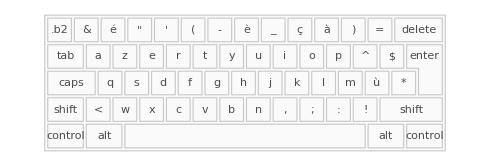

-Graphics-

```mathematica
LanguageIdentify["япон хэл"]
DictionaryLookup[All]
(* MMA所有词典语言 *)
Rasterize@ Style[#,Large]&@ Grid@ Partition[#,5,5,1,"\\"]&@LanguageData["Hebrew","Letters"]
(* 希伯来语字母表 *)
Rasterize@ Style[#,Large]&@ Grid@ Partition[#,5,5,1,"\\"]&@ LanguageData["Hindi","Letters"]
(* 印地语字母表 *)
DictionaryLookup[x__/;StringLength[x]>6]
(* 长度大于6的单词 *)
LanguageData["French","KeyboardImage"]
(* 法语键盘 *)
```

# IPA国际音标

```mathematica
Gather[WordData[#,"PhoneticForm"]&/@{"pay","bay","pray","prey","wade","weighed"}]
```

{{pˈeɪ},{bˈeɪ},{prˈeɪ,prˈeɪ},{wˈeɪd,wˈeɪd}}

# 字幕

## ffmpeg 命令转换字幕

```mathematica
(*
ffmpeg -i a.ass b.srt
ffmpeg -i c.vtt d.srt
ffmpeg -i e.lyric f.srt
rm -rf /usr/local/var/homebrew/locks
brew update
brew search ffmpeg
brew install ffmpeg
/usr/local/Cellar/ffmpeg/4.2.2_1
*)
```

```mathematica
ffmpegConvertAssToSrt:=With[
{
fname :=  FileNameJoin[{NotebookDirectory[], "[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass"}]
},
With[
{
dirname := DirectoryName@fname,
basename :=FileBaseName@fname
},
With[
{
strfilename := FileNameJoin[{dirname, basename <> ".srt"}]
},
With[
{
ffmpegCMD :=StringTemplate["ffmpeg -i \"`a`\" \"`b`\""][<|"a"->fname, "b"->strfilename|>],
ffmpegCMDList:= {"ffmpeg", "-i", fname, strfilename}
},
If[ FileExistsQ[strfilename],
DeleteFile[strfilename], (* 删除已存在的SRT 文件 *)
Nothing
];
Print@ffmpegCMDList;
RunProcess[ffmpegCMDList,ProcessEnvironment-><|"PATH"->"/usr/local/bin/"|>]
]
]
]
]
ffmpegConvertAssToSrt[]
```

{ffmpeg,-i,/Users/vvw/Documents/GitHub/doc/lang/programming/[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass,/Users/vvw/Documents/GitHub/doc/lang/programming/[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].srt}

<|ExitCode→0,StandardOutput→,StandardError→ffmpeg version 4.2.2 Copyright (c) 2000-2019 the FFmpeg developers
  built with Apple clang version 11.0.0 (clang-1100.0.33.16)
  configuration: --prefix=/usr/local/Cellar/ffmpeg/4.2.2_1 --enable-shared --enable-pthreads --enable-version3 --enable-avresample --cc=clang --host-cflags='-I/Library/Java/JavaVirtualMachines/adoptopenjdk-13.0.1.jdk/Contents/Home/include -I/Library/Java/JavaVirtualMachines/adoptopenjdk-13.0.1.jdk/Contents/Home/include/darwin -fno-stack-check' --host-ldflags= --enable-ffplay --enable-gnutls --enable-gpl --enable-libaom --enable-libbluray --enable-libmp3lame --enable-libopus --enable-librubberband --enable-libsnappy --enable-libtesseract --enable-libtheora --enable-libvidstab --enable-libvorbis --enable-libvpx --enable-libwebp --enable-libx264 --enable-libx265 --enable-libxvid --enable-lzma --enable-libfontconfig --enable-libfreetype --enable-frei0r --enable-libass --enable-libopencore-amrnb --enable-libopencore-amrwb --enable-libopenjpeg --enable-librtmp --enable-libspeex --enable-libsoxr --enable-videotoolbox --disable-libjack --disable-indev=jack
  libavutil      56. 31.100 / 56. 31.100
  libavcodec     58. 54.100 / 58. 54.100
  libavformat    58. 29.100 / 58. 29.100
  libavdevice    58.  8.100 / 58.  8.100
  libavfilter     7. 57.100 /  7. 57.100
  libavresample   4.  0.  0 /  4.  0.  0
  libswscale      5.  5.100 /  5.  5.100
  libswresample   3.  5.100 /  3.  5.100
  libpostproc    55.  5.100 / 55.  5.100
Input #0, ass, from '/Users/vvw/Documents/GitHub/doc/lang/programming/[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass':
  Duration: N/A, bitrate: N/A
    Stream #0:0: Subtitle: ass
Output #0, srt, to '/Users/vvw/Documents/GitHub/doc/lang/programming/[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].srt':
  Metadata:
    encoder         : Lavf58.29.100
    Stream #0:0: Subtitle: subrip (srt)
    Metadata:
      encoder         : Lavc58.54.100 srt
Stream mapping:
  Stream #0:0 -> #0:0 (ass (ssa) -> subrip (srt))
Press [q] to stop, [?] for help
size=      39kB time=00:23:34.22 bitrate=   0.2kbits/s speed=3.09e+05x    
video:0kB audio:0kB subtitle:26kB other streams:0kB global headers:0kB muxing overhead: 49.327991%
|>

/Users/vvw/Documents/GitHub/doc/lang/programming/[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass

```mathematica
(*Run["ffmpeg -i" <> ]*)
```

32512

```mathematica
(*

ASS 字幕开始的标志是："Dialogue: 0,"  或 "Dialogue: 1," 它们分别是两种不同的语言
比如："Dialogue: 0," 是日语，
"Dialogue: 1," 是中文

0:02:42.47,0:02:43.28,  开始时间,结束时间
   时[0-9]:分[0-5]

*)
```

```mathematica
jps//First
```

Dialogue: 0,0:02:42.47,0:02:43.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暗い

```mathematica
jps//First //StringCases[#, 
x:RegularExpression["\\d:[0-5]\\d:[0-5]\\d.\\d\\d"] ~~ ","~~
y:RegularExpression["\\d:[0-5]\\d:[0-5]\\d.\\d\\d"]~~__~~",,0,0,0,,"~~
z__->Sequence [x,y,z]]&
(*
SRT 字幕格式：
1
00:00:05,255-->00:00:06,654
...something they had never seen,

2
00:00:06,756-->00:00:08,087
which liberated a yellow,

*)
(* 
ASS 字幕格式：
"Dialogue: 0,0:02:42.47,0:02:43.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暗い"
"Dialogue: 1,0:02:42.47,0:02:43.28,TEXT-CN 浪漫雅圆,,0,0,0,,好黑"

ASS 字幕开始的标志是："Dialogue: 0,"  或 "Dialogue: 1," 它们分别是两种不同的语言
比如："Dialogue: 0," 是日语，
"Dialogue: 1," 是中文

0:02:42.47,0:02:43.28,  开始时间,结束时间

0:02:42.47  
\\d  0-9数字 时
[0-5] 0或5 分的十位
\\d  0-9数字 分的个位
\\d:[0-5]\\d 秒和分的格式一样 00-59
\\d\\d 00-99 秒的后面最大是99

StringCases["a13b12c17a32","a"~~x:RegularExpression["\\d+"]->x]
*)
(* 
ASS 转SRT ：
小时数从一位数字扩展成两位，比如：0 变成00
 毫秒数从两位数字扩展成三位，比如：99 变成990  

字符串格式化 StringTemplate 
	StringTemplate["first `a` then `b`"][<|"a"->1234,"b"->5678|>]

 *)
```

```mathematica
With[
{
ReplaceNewline :=StringReplace[#,"\n"->""]&,
ExtractTimeFromAss:= StringCases[#, 
x:RegularExpression["\\d:[0-5]\\d:[0-5]\\d.\\d\\d"] ~~ ","~~
y:RegularExpression["\\d:[0-5]\\d:[0-5]\\d.\\d\\d"]~~__~~",,0,0,0,,"~~
z__:>Sequence [x,y,z]]&
},
With[
{
AssDialogueFirstN:= MapIndexed[
Prepend[ExtractTimeFromAss@#1,First[#2]]&,
#assList~Take~#n
]&
(* 
  从ASS 文件抽出生成SRT 需要的信息：序号、开始时间、结束时间、文本
  命名参数是和“联合” (Association)结构一起用的，#name 是 #1[“name"] 的简写.
     #1 是函数的第一参   
   *)
},
With[
{
ListsToAssociation:=Association[Thread[Rule[#colNames,#alist]]]&
(*
   Convert Lists to Association
*)
},
With[
{
jpsDataset:=Dataset@Map[ListsToAssociation[<|"colNames"->{"order","beginTime","endTime","text"}, "alist"->#|>]&, AssDialogueFirstN[<|"assList"-> Map[ReplaceNewline,jps], "n"->All|>]],
chsDataset:=Dataset@Map[ListsToAssociation[<|"colNames"->{"order","beginTime","endTime","text"}, "alist"->#|>]&, AssDialogueFirstN[<|"assList"->  Map[ReplaceNewline,chs], "n"->All|>]]
(* Ass 中日字幕数据集 *)
},

With[
{
AssTimeToSrtTime:=First@StringCases[#, 
x:RegularExpression["[0-9]{0,1}"]~~y:RegularExpression["[0-9]{1}"]~~
(* 前两位数字：小时，x可以没有 *)
":"~~mm:RegularExpression["[0-9]{2}"]~~
(* 分 *)
":"~~ss:RegularExpression["[0-9]{2}"]~~
(* 秒 *)
c:"."~~
res___ :>(If[x=="","0",x]<>y<>":"<>mm<>":"<>ss<>","<>res<>"0")]&
(* 
	Ass 时间转 Srt 时间 
  SRT
	00:00:05,255-->00:00:06,654
   ASS
	0:02:42.47,0:02:43.28
*)
},
(* 
ASS 转SRT ：
小时数从一位数字扩展成两位，比如：0 变成00
 毫秒数从两位数字扩展成三位，比如：99 变成990  

RegularExpression["."]  正规表达式 匹配任意一个字符，换行除外
Shortest[__~~"\n\n"]  最短匹配

tutorial/StringPatterns
	DigitCharacterpaclet:ref/DigitCharacter 数字0 到9

x:RegularExpression["[0-9]{0,1}"]  数字0-9 重复0到1 次
匹配小时数的十位数，如果是0，ASS 格式字幕会忽略不写
   所以它的重复次数可以是0
y:RegularExpression["[0-9]{1}"]
 匹配小时数的个位数，一定是0-9之间的一个数字
  所以它的重复次数是1

{{2,2},{2,2}}/.x:{2..}:>(x/._Integer?(#==2&)->3)

字符串格式化 StringTemplate 
	StringTemplate["first `a` then `b`"][<|"a"->1234,"b"->5678|>]

 *)
With[
{
jpsSrtDataset:=jpsDataset[All, {"beginTime"->AssTimeToSrtTime, "endTime"->AssTimeToSrtTime}],
chsSrtDataset:=chsDataset[All, {"beginTime"->AssTimeToSrtTime, "endTime"->AssTimeToSrtTime}],
SrtLine:=StringTemplate["`order`\n`beginTime` --> `endTime`\n`text`\n"][#]&,
(*
生成一行SRT 字幕文本：
  input:<|"order"->1,"beginTime"->"00:02:42,470","endTime"->"00:02:43,280","text"->"暗い\n"|>
output: SRT Text line
*)
ExtractInfoFromMecabText:= StringCases[ #,
Shortest[
word__~~"	"~~
pinci__~~","~~
__~~","~~__~~","~~__~~","~~__~~","~~__~~","~~__~~","~~__~~","
~~ Longest[pinyin__]

]:>Sequence[word,pinyin,pinci] ]&,
(* 从Mecab 分词结果中提取出需要的信息 *)

MecabJapaneseSegment := FromCharacterCode[ToCharacterCode[RunProcess[{"bash","-c",StringTemplate[ "echo \"`jpaText`\" | /usr/local/bin/mecab"][ <|"jpaText"->#|>]},"StandardOutput",ProcessDirectory->$InstallationDirectory]],"UTF-8"]&
(* stdin 读出来的字节流好像确实是utf8字符编码，但是不知为什么必须转一次才正常 *)
(*FromCharacterCode[BinaryReadList@file,"UTF-8"]*)
(*调用外部程序Mecab 执行日语分词*)
},
With[
{
SrtText:=StringJoin@Map[SrtLine]@Normal@#&,
assFullPath := FileNameJoin[{NotebookDirectory[], "[Kamigami] Shoujo Shuumatsu Ryokou - 01 [1080p x265 AAC].ass"}],
elementAllLenght1Q:= Scan[ If[StringLength[First[#]]>1,Return[False]] &,#]===Null&,
(* 列表里面的列表元素长度全是1 *)
	(* Scan 除非主动Return 否则返回值是Null 利用这点进行逻辑判断 *)
JapaneseSegment:= Module[
{
segs,mecabInfos,
ReplaceEOS:=(# /. x_String/;StringContainsQ[x, "EOS"]->Nothing)&,
SegmentToAssociation:= ListsToAssociation[
<|"colNames"->{"MecabWord","MecabPinyin","MecabPinci"}, 
"alist"->#|>
]& 
(* 分词数据集 *)
},

segs = MecabJapaneseSegment[#];
(*Mecab 日语分词*)
segs=StringSplit[segs,RegularExpression["(?m)^"]];
(*Split 字符串在换行处*)
segs=ReplaceEOS /@ segs;
(* 去掉包含EOS 的项 *)
segs=  ReplaceNewline/@ segs;
(* 去掉换行符 *)

mecabInfos = ExtractInfoFromMecabText /@ segs;
(* 从Mecab 分词结果中提取出需要的信息 *)


mecabInfos = DeleteCases[mecabInfos, x_List/;( Length[x]==0 ||   First[x]=="　") ];
mecabInfos  /. {}->Nothing;
(* 
	{} 空列表删掉
   {"　", "　", "記号"} 空白词头删掉
 *)

Map[SegmentToAssociation, mecabInfos]

]&
(* 日语分词 *)
},

text = SrtText@jpsSrtDataset;
dirname := DirectoryName@assFullPath;
basename:= FileBaseName@assFullPath;
strfilename := FileNameJoin[{dirname, basename <> ".srt"}];
If[ FileExistsQ[strfilename],
DeleteFile[strfilename], (* 删除已存在的SRT 文件 *)
Nothing
];
Export[strfilename,text,"Text",CharacterEncoding->"UTF8"];
(* 导出SRT 文件 *)

text =Map[#text&]@ Normal[jpsSrtDataset];
jpsegs = Map[JapaneseSegment,text];
jpsegsDataset=Map[Dataset, jpsegs, {1}];
(*jpsegs = DeleteCases[jpsegs, x_List/;elementAllLenght1Q[x] ];*)  (* 删除列表里元素长度全是1的列表 *)

If[ Length@jpsegsDataset===Length@jpsSrtDataset,
Print["### Checking dataset's Length okay. "], Throw["### ERROR: dataset's Length not equal!"]];
(* 检查数据集的长度是否一至，不一至就抛错误 *)

(*"点け"*)
(* 查JISHO 数据 *)

jpsegsDataset[[1;;10]]//Column//Print;

Column[
{
jpsSrtDataset,
chsSrtDataset
}
]

]

]

]


]

]

]
]
```

### Checking dataset's Length okay.

Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]
Dataset[<>]

Dataset[<>]
Dataset[<>]

```mathematica
DeleteCases[ {{"く", "ク", "形容詞"}, {},{"　", "　", "記号"}, {"ら", "ラ", "名詞"}, {}, {"い", "イ", "動詞"},{"暗い", "クライ", "形容詞"}},
x_List/;( Length[x]==0 ||   First[x]=="　"|| StringLength[First[x]]==1 )]//InputForm
```

{{"暗い", "クライ", "形容詞"}}

```mathematica
StringLength["く"]
```

1

# 爬JISHO日语单词及音频

```mathematica
(*

MMA 爬虫 
WebDriverChrome 已过时
WebExecute 现在的
Python 爬虫
https://www.hi-pda.com/forum/viewthread.php?tid=2670375&from=favorites
	driver.find_element_by_class_name('concept_light-status_link show_inflection_table').click()
一小时获取B站全站视频数据——高速网络爬虫的设计
	https://zhuanlan.zhihu.com/p/35359905
	https://github.com/uupers/BiliSpider

	tableText=WebExecute[browser,"JavascriptExecute"->"return document.getElementById('table_id').innerText;"];
	
	
MMA stdin 命令行文互
	https://reference.wolfram.com/language/ref/ProcessConnection.html

epwing 字典文本提取
	https://github.com/FooSoft/zero-epwing

Mecab 日语分词
	echo "じゃあランタン点けていいですか" | mecab
   rm-rf/usr/local/var/homebrew/locks
	      brew search mecab
		  brew install mecab
		  brew install mecab-ipadic
		https://pypi.org/project/mecab-python3

 JISHO API 【nodejs】
	 https://jisho.org/api/v1/search/words?keyword=点け&page=1
	 https://github.com/cckelly/jisho.js  能下载mp3
	   https://github.com/mistval/unofficial-jisho-api

查日语句子
	https://jisho.org/search/じゃあランタン点けていいですか

Show inflections 按钮
	JavaScript 执行点击 【Chrome 控制台里面执行】
	document.getElementsByClassName ('concept_light-status_link show_inflection_table')[0].click()

弹窗的完整单词活用形
	document.getElementsByClassName ("modal_content")[0]

*)
Module[
{
ASSERT,
segs,url,rawjson
},

ASSERT[statusCode_]:= If[statusCode=!=200,   Message[ASSERT::statusErr, 200];Abort[],  Print@"----- ASSERT statusCode Okay."];
ASSERT::statusErr="network errors: status not equal `1`";

segs =RunProcess[{"bash","-c","echo \"じゃあランタン点けていいですか\" | /usr/local/bin/mecab"},"StandardOutput",ProcessDirectory->$InstallationDirectory];
segs=FromCharacterCode[ToCharacterCode[a],"UTF-8"];  (* stdin 读出来的字节流好像确实是utf8字符编码，但是不知为什么必须转一次才正常 *)
(*FromCharacterCode[BinaryReadList@file,"UTF-8"]*)
(* Mecab 分词 *)

Print@segs;

url=StringTemplate["https://jisho.org/api/v1/search/words?keyword=`keyword`&page=`page`"][
<|"keyword"->URLEncode["点け"], "page"->1|>
];

rawjson=Import[url,"RawJSON"];



ASSERT[rawjson["meta"]["status"]];


(*占位符 `1`*)
Print@rawjson;
Print@rawjson["data"][[1]]["slug"];
Print@rawjson["data"][[1]]["jlpt"][[1]];
Print@rawjson["data"][[1]]["japanese"][[1]];
Print@rawjson["data"][[1]]["senses"][[1]]["english_definitions"];
Print@rawjson["data"][[1]]["senses"][[1]]["parts_of_speech"];
Print@rawjson["data"][[1]]["senses"][[1]]["see_also"];
]
```

じゃあ	接続詞,*,*,*,*,*,じゃあ,ジャア,ジャー
ランタン	名詞,一般,*,*,*,*,ランタン,ランタン,ランタン
点け	動詞,自立,*,*,五段・カ行イ音便,仮定形,点く,ツケ,ツケ
て	助詞,接続助詞,*,*,*,*,て,テ,テ
いい	形容詞,非自立,*,*,形容詞・イイ,基本形,いい,イイ,イイ
です	助動詞,*,*,*,特殊・デス,基本形,です,デス,デス
か	助詞,副助詞／並立助詞／終助詞,*,*,*,*,か,カ,カ
EOS

----- ASSERT statusCode Okay.

<|meta→<|status→200|>,data→{<|slug→点ける,is_common→True,tags→{wanikani8},jlpt→{jlpt-n2},japanese→{<|word→点ける,reading→つける|>},senses→{<|english_definitions→{to turn on,to switch on,to light up},parts_of_speech→{Ichidan verb,Transitive verb},links→{},tags→{Usually written using kana alone},restrictions→{},see_also→{付ける つける},antonyms→{},source→{},info→{}|>},attribution→<|jmdict→True,jmnedict→False,dbpedia→False|>|>,<|slug→つけっ放し,is_common→False,tags→{},jlpt→{},japanese→{<|word→付けっぱなし,reading→つけっぱなし|>,<|word→つけっ放し,reading→つけっぱなし|>,<|word→点けっぱなし,reading→つけっぱなし|>,<|word→付けっ放し,reading→つけっぱなし|>,<|word→点けっ放し,reading→つけっぱなし|>},senses→{<|english_definitions→{leaving a device on (e.g. TV, air conditioner),leaving something engaged (e.g. a key in a lock)},parts_of_speech→{Noun},links→{},tags→{Usually written using kana alone},restrictions→{},see_also→{っぱなし},antonyms→{},source→{},info→{}|>},attribution→<|jmdict→True,jmnedict→False,dbpedia→False|>|>}|>

点ける

jlpt-n2

<|word→点ける,reading→つける|>

{to turn on,to switch on,to light up}

{Ichidan verb,Transitive verb}

{付ける つける}

```mathematica
debug@VoiceStyleData(*TextRecognize*)
```

9sm2e_shm25FrontEndObject[LinkObject["9sm2e_shm", 3, 1]]25System`VoiceStyleData

```mathematica
(*
Highlight and speak each substring
TTS 时高亮文本
*)
lst = {"Ooops!","there","are","errors"};
Monitor[Do[Speak[lst[[i]]];Pause[0.8],{i,Length[lst]}],
Row[MapAt[Style[#,CMYKColor[0,0.4,1,0]]&,lst,If[IntegerQ[i],i,1]],"  "]]
```

```mathematica
(*TTS 可用性别和语言列表*)
(*VoiceStyleData[]//Dataset*)

(*TTS 指定的性别和语言列表*)
VoiceStyleData[#Gender=="Female"&& (#Language=="English" ||
 #Language=="Japanese" ||
#Language=="Chinese" ||
#Language=="French" 
 )&]//Dataset
```

Dataset[<>]

```mathematica
(*
0.952941
0.67451
0.227451
RGBColor[0.952941,0.67451, 0.227451,1]
teal blue 蓝绿色 w3.css  https://www.w3schools.com/w3css/default.asp
*)
```

```mathematica
AudioPlay@SpeechSynthesize["すみません！",<|"Name"->"Kyoko","Language"->"Japanese"|>];
```

```mathematica
voiceStypes=$VoiceStyles
Monitor[Do[AudioPlay@SpeechSynthesize["Hello, I'm Chinese.",voiceStypes[[i]]];Pause[1.5],{i,Length[voiceStypes]}],
Row[MapAt[Style[#,RGBColor[0.95,0.67, 0.23,1]]&,voiceStypes,If[IntegerQ[i],i,1]],"  "]]
```

{AlanWBlack,Alex,Alice,Alva,Amelie,Anna,Carmit,Damayanti,Daniel,Diego,Ellen,Fiona,Fred,Ioana,Joana,Jorge,Juan,Kanya,Karen,KevinLenzo,KevinLenzo16,Kyoko,Laura,Lekha,Luca,Luciana,Maged,Mariska,Mei-Jia,Melina,Milena,Moira,Monica,Nora,Paulina,Rishi,RMS,Samantha,Sara,Satu,Sin-ji,SLT,Tessa,Thomas,Ting-Ting,Veena,Victoria,Xander,Yelda,Yuna,Yuri,Zosia,Zuzana}

$Aborted

```mathematica
(*
Rule  String -> String,
Rule  String -> List[Rule],
Rule  String -> List[ List[ Rule ] ]
List[List]
*)

Module[{ret}, ret={}; (*有一个内部变量*)
f[x_String->y_String]:= Print[Sow[x], "--->", y,","];
f[x_String->y_List]:=(Print[Sow[x], "->{"];Scan[f,y];Print["}"]);
f[x_List]:= (Print["{"];Scan[f,x];Print["}"]);
f[___]:=( Message[f::errTemplate, "function name??"];Abort[];);
f::errTemplate:= "Ooops!there ars errors in `1`"
]
(*f[x_String->y_List]:= Print[x, "--->", f[]]*)
Reap@f[j(*"a"->{{"b"->"c"}}*)]
```

{Null,{{charCode,discCode,subbooks,title,copyright,entries,heading,text}}}

```mathematica
(*First[j]
Rest[j]*)
```

```mathematica
(*"提取学研国語大辞典所有活用形"*)
Module[{resultCatch={},item},
For[i=1,i< Length@jj["subbooks"][[1]]["entries"]+1,i++,
item=jj["subbooks"][[1]]["entries"][[i]];
(*Print@Keys[item][[2]]=="text";*)
If[
   Length[ Keys[item]]>1&& Keys[item][[2]]=="text" &&StringContainsQ[item["text"],"形式名 活用形 下接語例"], (*会出现只有heading 没有text的情况*)
AppendTo[resultCatch, First@StringCases[item["text"], Shortest[__~~"\n\n"]]]  (*First 取活用不要解释*)
];
];
(*First@StringCases[item["text"], Shortest[__~~"\n\n"]]//InputForm*)
(*item["text"]//InputForm*)
resultCatch
]
```

{アーケイック 形容動詞
形式名 活用形 下接語例
未然形 アーケイック・だろ {う}
連用形 アーケイック・だっ {た/ない}
　　　 アーケイック・に
　　　 アーケイック・で
終止形 アーケイック・だ {。}
連体形 アーケイック・な {とき}
仮定形 アーケイック・なら {ば}
命令形 ―

,アース 自動詞他動詞。「する」と結合してサ変動詞としても用いる
形式名 活用形 下接語例
未然形 アース・し {ない}
　　　 アース・せ
　　　 アース・さ
連用形 アース・し {ます/た}
終止形 アース・する {。}
連体形 アース・する {とき}
仮定形 アース・すれ {ば}
命令形 アース・しろ {。}
　　　 アース・せよ

,アーティフィシャル 形容動詞
形式名 活用形 下接語例
未然形 アーティフィシャル・だろ {う}
連用形 アーティフィシャル・だっ {た/ない}
　　　 アーティフィシャル・に
　　　 アーティフィシャル・で
終止形 アーティフィシャル・だ {。}
連体形 アーティフィシャル・な {とき}
仮定形 アーティフィシャル・なら {ば}
命令形 ―

,あいあい【哀哀】 形容動詞トタル型活用
形式名 活用形 下接語例
未然形 ―
連用形 ― {ない}
　　　 ―
　　　 あいあい・と
終止形 ―
連体形 あいあい・たる {とき}
仮定形 ―
命令形 ―

,あいあい【〓曖〓曖】 形容動詞トタル型活用
形式名 活用形 下接語例
未然形 ―
連用形 ― {ない}
　　　 ―
　　　 あいあい・と
終止形 ―
連体形 あいあい・たる {とき}
仮定形 ―
命令形 ―

,あいあい【〓藹〓藹】 形容動詞トタル型活用
形式名 活用形 下接語例
未然形 ―
連用形 ― {ない}
　　　 ―
　　　 あいあい・と
終止形 ―
連体形 あいあい・たる {とき}
仮定形 ―
命令形 ―

,23135,わるふざけ【悪ふざけ】 自動詞。「する」と結合してサ変動詞としても用いる
形式名 活用形 下接語例
未然形 わるふざけ・し {ない}
　　　 わるふざけ・せ
　　　 わるふざけ・さ
連用形 わるふざけ・し {ます/た}
終止形 わるふざけ・する {。}
連体形 わるふざけ・する {とき}
仮定形 わるふざけ・すれ {ば}
命令形 わるふざけ・しろ {。}
　　　 わるふざけ・せよ

,わるよい【悪酔(い)】 自動詞。「する」と結合してサ変動詞としても用いる
形式名 活用形 下接語例
未然形 わるよい・し {ない}
　　　 わるよい・せ
　　　 わるよい・さ
連用形 わるよい・し {ます/た}
終止形 わるよい・する {。}
連体形 わるよい・する {とき}
仮定形 わるよい・すれ {ば}
命令形 わるよい・しろ {。}
　　　 わるよい・せよ

,われかえ・る【割れ返る】 自動詞五段活用［ラ行］
形式名 活用形 下接語例
未然形 われかえ・ら {ない/う}
　　　 われかえ・ろ
連用形 われかえ・り {ます/た}
　　　 われかえ・っ
終止形 われかえ・る {。}
連体形 われかえ・る {とき}
仮定形 われかえ・れ {ば}
命令形 われかえ・れ {。}

,わ・れる【割れる】 自動詞下一段活用［ラ行］
形式名 活用形 下接語例
未然形 わ・れ {ない}
連用形 わ・れ {ます/た}
終止形 わ・れる {。}
連体形 わ・れる {とき}
仮定形 わ・れれ {ば}
命令形 わ・れろ {。}
　　　 わ・れよ

,ワンパターン 形容動詞
形式名 活用形 下接語例
未然形 ワンパターン・だろ {う}
連用形 ワンパターン・だっ {た/ない}
　　　 ワンパターン・に
　　　 ワンパターン・で
終止形 ワンパターン・だ {。}
連体形 ワンパターン・な {とき}
仮定形 ワンパターン・なら {ば}
命令形 ―

}
 |  |  |  |

```mathematica
Export[FileNameJoin[{$HomeDirectory,"/Documents/GitHub/ebmac/","JPHuoYong.json"}],%]
```

/Users/vvw/Documents/GitHub/ebmac/JPHuoYong.json

```mathematica
(*closure 闭包*)
add=Module[{y},y=0;Function[x, y=y+x]];
add /@ {1,2,3}
```

```mathematica
Head /@{"charCode","discCode","subbooks"}
```

{String,String,String}

```mathematica
( # /. (x__->y__):> (x->(
If[ListQ[y],y//First, y]
)) )& /@ j
```

```mathematica
Scan[Print, {1,2}]
```

1

2

```mathematica
(*利用Scan 的副作用实现计算*)
data =Table[Random[],{100}];  (*一百个包含0～1之间的实数List*)
hint = Table[0,{5}]  (* List[0,0,0,0,0] *)
Scan[ hint[[Ceiling[# 5]]]++&, data ]
(*Ceiling[5 #]  5 * 0~1之间的实数，得到0~5 之间的实数，Ceiling 上取整，得到0 ~ 5 之间的整数*)
(* a++ 先返回a, 然后a = a + 1*)
hint
```

{0,0,0,0,0}

{24,18,19,21,18}

```mathematica
myOddQ[x_] := ( Print["debug:"<>TextString@{x, OddQ[x]}]; OddQ[x] ) (*打印调试信息的小技巧*)
And@@myOddQ/@{1,2,3}  (*Apply 替换Head, f@@{1,2} List[1,2] 中的List 被替换为f*)
Scan[If[myOddQ[#], True, Return[False] ]&, {1,3,5}]==Null 
(*Scan 除非主动Return 否则返回值是Null 利用这点进行逻辑判断*)
```

debug:{1, True}

debug:{2, False}

debug:{3, True}

False

debug:{1, True}

debug:{3, True}

debug:{5, True}

True

```mathematica
{{2,2},{2,2}}/.x:{2..}:>(x/._Integer?(#==2&)->3)
```

{{3,3},{3,3}}

{1, True}

{3, True}

{5, True}

True

```mathematica
(*



Scan
Scan不是一个pure funtion，和Map 很像，但是不返回list结果。Scan 和Return 函数配合使用更具威力，一遇到Return的返回值Scan 就终止并返回那个值。

Head
给出表达示的类型
Map[Head,{3,3/2,3+2I,{3,2},a}]
{Integer,Rational,Complex,List,Symbol}

Intersection[{2,-2,1,3,1},{2,1,-2,-1},SameTest->(Abs[#1]==Abs[#2]&)]

{a,b,c}∩{b,c,d}

*)
```

```mathematica
{c,b,a}∩{b,a,c}
```

{a,b,c}

```mathematica
sameQ :=(Length[#1 ∩ #2]  == Length[ #1])&
sameQ[{1,2,3}, {1,3,2}]
```

True

```mathematica
$Version
```

12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019)

```mathematica
TreeForm@{"charCode"->"jisx0208","discCode"->"epwing","subbooks"->{"a"->"b"}}
```

```mathematica
?ExportString
```

```mathematica
GeneralUtilities`PrintDefinitions[ExportString]
```

ies2a_shm32FrontEndObject[LinkObject["ies2a_shm", 3, 1]]32System`ExportString

```mathematica
TextRecognize[#,"Word",{"Text", "BoundingBox"}, Language->"Chinese" ]& @ -Graphics-
```

{{分别任中心的主任和副主任。,Rectangle[{10,13},{384,41}]},{经过十几年,在汪容和中心全体成员,Rectangle[{405,13},{881,41}]}}

```mathematica
i = -Graphics-;
res=TextRecognize[i,"Line","BoundingBox"]
HighlightImage[i,{"Boundary",EdgeForm[{Red,Opacity[.3]}],res}]
```

{Rectangle[{6,135},{346,149}],Rectangle[{5,80},{663,94}],Rectangle[{6,61},{94,75}],Rectangle[{6,27},{671,41}],Rectangle[{6,8},{408,22}]}

-Graphics-

```mathematica
debug@TextRecognize
```

cv47s_shm33FrontEndObject[LinkObject["cv47s_shm", 3, 1]]33System`TextRecognize

```mathematica
(*
单词IPA发音
https://mathematica.stackexchange.com/questions/34391/split-lingusticipa-at-words-unique-sounds
https://mathematica.stackexchange.com/questions/32148/find-a-words-linguistic-pronunciation

重载系统函数的黑科技
https://mathematica.stackexchange.com/questions/18187/overloading-second-argument-of-countrydata
[dictionary.com](https://www.dictionary.com/e/word-of-the-day/)


[dictionary.com](https://www.dictionary.com/e/word-of-the-day/)

# happy 

[ **hap**-ee] PHONETIC RESPELLING

/ˈhæp i/IPA  



*)
```

```mathematica
Gather[WordData[#,"PhoneticForm"]&/@{"pray","prey","wade","weighed"}]
```

{{prˈeɪ,prˈeɪ},{wˈeɪd,wˈeɪd}}

```mathematica
RGBColor[0.952941,0.67451, 0.227451,1]
i=-Graphics-
i//ImageDimensions
```

{765,12909}

```mathematica
ImageTake[i,{255,2110},{1,-1}]//Export["vis-à-vis-dictionary.com.png",#]&
```

```mathematica
"vis-à-vis-dictionary.com.png"
```

vis-à-vis-dictionary.com.png

```mathematica
(*SystemOpen[DirectoryName[AbsoluteFileName["vis-à-vis-dictionary.com.png"]]]*)
```

```mathematica
$SystemID
```

```mathematica
DLLTable={"MacOSX-x86-64"->{FileNameJoin[{$InstallationDirectory,"SystemFiles","Links","MP3Tools","LibraryResources","MacOSX-x86-64"}]}}
dlls=Cases[DLLTable,($SystemID->l_):>l]
```

{MacOSX-x86-64→{/Applications/Mathematica.app/Contents/SystemFiles/Links/MP3Tools/LibraryResources/MacOSX-x86-64}}

{{/Applications/Mathematica.app/Contents/SystemFiles/Links/MP3Tools/LibraryResources/MacOSX-x86-64}}

```mathematica
Unevaluated
```

```mathematica
PacletInstall["BTools","Site"->"http://www.wolframcloud.com/objects/b3m2a1.paclets/PacletServer"]
```

Paclet[BTools,2.1.52,<>]

```mathematica
FileNameJoin[{$HomeDirectory,"cegfdb","tutorial"}]
```

/Users/vvw/cegfdb/tutorial

```mathematica
WebSiteBuild[FileNameJoin[{$HomeDirectory,"cegfdb","tutorial"}],Automatic]
```

/Users/vvw/cegfdb/tutorial/output

```mathematica
(*SpeechSynthesisTools`Private`SpeechDump`stringToAssoc*)
stringToAssoc[s_?StringQ,Optional[numerics_,{}]]:=Quiet[Check[Association[Replace[Rule@@@Map[StringSplit[#,":"]&,StringSplit[s,"\n"]],Rule[x_,y_]/;MemberQ[numerics,x]:>(x->ToExpression[y]),{1}]],s]];
stringToAssoc[s_?FailureQ,___]:=s;
stringToAssoc[___]:=$Failed;
```

```mathematica
Module[{labels,fields,cipherKey,textIn,codeOut,clear,clearFields,encrypt,encryptText},clearFields[]:=(cipherKey=textIn=codeOut="");
encryptText[]:=(codeOut=textIn);(*placeholder*)labels={"PASSWORD","PLAINTEXT","CIPHERTEXT"};
fields={InputField[Dynamic@cipherKey,String],InputField[Dynamic@textIn,String],InputField[Dynamic@codeOut,String,Enabled->False]};
clear=Button["Clear",clearFields[],ImageSize->All];
encrypt=Button["Encrypt",encryptText[],ImageSize->All];
clearFields[];
Panel[TableForm[Join[Transpose[{labels,fields}],{{clear,encrypt}}],TableAlignments->{Right,Left}],Style["Playfair Encrypter",12,Bold]]]
```

PASSWORD | 
PLAINTEXT | 
CIPHERTEXT | 
Clear | EncryptPlayfair Encrypter

```mathematica
Deploy["You cannot select individual words or letters in this text"]
```

You cannot select individual words or letters in this text

```mathematica
(*创建一个不显示的文档*)
nb=CreateDocument[Table[TextCell["text "<>ToString[k],"Text"],{k,5}],Visible->False];
(*您可以执行笔记本操作，甚至当它不可视时*)
SelectionMove[nb,Next,CellContents];
NotebookRead[nb]
```

text 1

```mathematica
(*使笔记本可视化*)
SetOptions[nb,Visible->True]
```

```mathematica
(*当按下该按钮时，粘贴 expr.*)
PasteButton[Defer[2+2]]
```

2+2

```mathematica
Map[f,{{1,2},{3,4}},{1,0}]
```

{{1,2},{3,4}}

```mathematica
(*
递归查找所有文件，全打印出来
find . -type f | xargs cat


find . -type f | awk -F "/" '{print "put ",$NF}'
ls-1<dir> | xargs-n1-i%f echo'put %f'
*)
```

```mathematica
jps
```

{Dialogue: 0,0:02:42.47,0:02:43.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暗い
,Dialogue: 0,0:02:44.29,0:02:44.99,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暗い
,Dialogue: 0,0:02:45.78,0:02:46.62,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暗い
,Dialogue: 0,0:02:49.28,0:02:52.58,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,くーらーいー
,Dialogue: 0,0:02:53.60,0:02:54.29,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うるせえ
,Dialogue: 0,0:02:55.44,0:02:56.15,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ごめん
,Dialogue: 0,0:02:58.00,0:02:58.64,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いいよ
,Dialogue: 0,0:03:01.98,0:03:04.24,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,じゃあ　ランタン点けていいですか
,Dialogue: 0,0:03:04.61,0:03:05.17,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ダメ
,Dialogue: 0,0:03:06.04,0:03:07.11,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そんな
,Dialogue: 0,0:03:07.97,0:03:09.09,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,節約しろ
,Dialogue: 0,0:03:09.42,0:03:12.58,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,給油施設だって次どこにあるか分からないんだぞ
,Dialogue: 0,0:03:16.46,0:03:21.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,でもまあ　ずっと暗闇だから　目が慣れてきたかも
,Dialogue: 0,0:03:22.21,0:03:24.92,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,もうずっと日の光を見てないからね
,Dialogue: 0,0:03:26.43,0:03:27.87,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,何日経ったかすら…
,Dialogue: 0,0:03:28.37,0:03:32.38,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いやホント　どこにいるんだろうね　私たち
,Dialogue: 0,0:03:34.54,0:03:36.74,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,なんでこんな所にいるんだっけ
,Dialogue: 0,0:03:37.19,0:03:42.04,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ユー　お前な　あの穴に入ってみようとか言ってたのは誰ですか
,Dialogue: 0,0:03:44.28,0:03:45.20,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃんだっけ
,Dialogue: 0,0:03:45.22,0:03:46.15,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,お前だよ
,Dialogue: 0,0:03:48.29,0:03:51.98,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あれは　ほら　古い言葉にもあるじゃん
,Dialogue: 0,0:03:52.34,0:03:55.67,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,確か「穴があったら入りたい」って
,Dialogue: 0,0:03:56.24,0:03:59.24,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そういう意味の言葉だっけ　それ
,Dialogue: 0,0:04:05.23,0:04:07.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,とにかく出口を見つけないと
,Dialogue: 0,0:04:07.88,0:04:10.54,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,食べ物もあんまりないしねー
,Dialogue: 0,0:04:10.84,0:04:15.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,まあ　出たとこで　食料が手に入るか分からないしね
,Dialogue: 0,0:04:17.32,0:04:20.13,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,どうなるんだろうね　私たち
,Dialogue: 0,0:04:24.10,0:04:26.38,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いつになったら一番上に
,Dialogue: 0,0:04:28.87,0:04:29.41,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ねえ
,Dialogue: 0,0:04:42.31,0:04:43.70,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,私も寝よう
,Dialogue: 0,0:05:24.12,0:05:25.05,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ど…どうも
,Dialogue: 0,0:05:26.31,0:05:29.09,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,スープだって　どんな感じで？
,Dialogue: 0,0:05:29.16,0:05:31.20,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ああ　それだったら
,Dialogue: 0,0:05:44.15,0:05:45.52,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,暖かい
,Dialogue: 0,0:05:49.60,0:05:51.19,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,お腹すいた
,Dialogue: 0,0:06:49.25,0:06:50.40,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,さむ
,Dialogue: 0,0:07:32.71,0:07:33.93,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,風が吹いてる
,Dialogue: 0,0:07:40.26,0:07:41.73,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ねえ　起きて
,Dialogue: 0,0:07:42.16,0:07:44.36,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,おい　ユー
,Dialogue: 0,0:07:54.40,0:07:57.16,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そう　風が吹く方に進んでいけば…
,Dialogue: 0,0:07:57.83,0:07:59.71,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,出口があるってこと？
,Dialogue: 0,0:08:00.47,0:08:01.40,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そういうこと
,Dialogue: 0,0:08:17.80,0:08:18.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,どう
,Dialogue: 0,0:08:22.08,0:08:22.59,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あっち
,Dialogue: 0,0:08:23.41,0:08:23.99,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,よし
,Dialogue: 0,0:08:33.56,0:08:34.71,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,次はあっち
,Dialogue: 0,0:08:35.27,0:08:35.95,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,分かった
,Dialogue: 0,0:08:47.57,0:08:48.48,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,光だ
,Dialogue: 0,0:09:33.87,0:09:34.63,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,すごい
,Dialogue: 0,0:09:35.35,0:09:37.16,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,明るいよ　ちーちゃん
,Dialogue: 0,0:09:45.43,0:09:46.61,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,夜だったんだ
,Dialogue: 0,0:10:01.20,0:10:05.49,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ねえ　せっかく外に出たんだし　スープ飲もうよ　スープ
,Dialogue: 0,0:10:06.71,0:10:09.24,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,じゃあ　出られた記念ということで
,Dialogue: 0,0:10:09.42,0:10:10.83,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,やったー　ご飯
,Dialogue: 0,0:10:19.00,0:10:20.22,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,もういいんじゃない
,Dialogue: 0,0:10:20.98,0:10:21.66,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そうだな
,Dialogue: 0,0:10:31.99,0:10:34.60,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,はい　最後の１缶だからな
,Dialogue: 0,0:10:35.40,0:10:35.75,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うん
,Dialogue: 0,0:10:36.50,0:10:37.19,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あちっ
,Dialogue: 0,0:10:44.93,0:10:46.33,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,おいしいー
,Dialogue: 0,0:10:51.98,0:10:55.95,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,知らなかったね　夜がこんなに明るいなんて
,Dialogue: 0,0:10:56.93,0:10:59.62,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ずっと暗い穴の中にいたからね
,Dialogue: 0,0:10:59.88,0:11:01.76,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,光に敏感になってるんだよ
,Dialogue: 0,0:11:02.37,0:11:05.98,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,じゃあ　これで日が昇ってきたらどうなっちゃうの
,Dialogue: 0,0:11:07.38,0:11:08.24,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,焼け死ぬ
,Dialogue: 0,0:11:11.75,0:11:12.53,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うるさい
,Dialogue: 0,0:12:16.09,0:12:16.75,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ヒット
,Dialogue: 0,0:12:19.30,0:12:19.96,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ヒット
,Dialogue: 0,0:12:24.99,0:12:25.70,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,外れ
,Dialogue: 0,0:12:29.88,0:12:30.34,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ありゃ
,Dialogue: 0,0:12:33.51,0:12:34.60,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,じゃあ　ラスト
,Dialogue: 0,0:12:35.39,0:12:37.00,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,もっと撃ってもいいよ
,Dialogue: 0,0:12:44.56,0:12:45.13,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ヒット
,Dialogue: 0,0:12:51.43,0:12:52.00,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ヒット
,Dialogue: 0,0:12:58.56,0:12:59.08,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ヒット
,Dialogue: 0,0:13:00.62,0:13:02.12,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃんも撃つかい
,Dialogue: 0,0:13:02.70,0:13:04.22,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いや　私はいい
,Dialogue: 0,0:13:05.36,0:13:06.79,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,下手くそだもんね
,Dialogue: 0,0:13:07.42,0:13:08.64,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うるさいな
,Dialogue: 0,0:13:09.13,0:13:11.15,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃんは武器持たないの？
,Dialogue: 0,0:13:11.55,0:13:12.88,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いらないよ　そんなの
,Dialogue: 0,0:13:18.48,0:13:20.10,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,たくさんあるのに
,Dialogue: 0,0:13:20.66,0:13:22.09,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ほとんどゴミでしょう
,Dialogue: 0,0:13:22.96,0:13:26.11,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,でもまあ　もう少し探索してみようか
,Dialogue: 0,0:13:27.84,0:13:32.14,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,武器じゃなくてもさ　使えるものがあるかもしれない
,Dialogue: 0,0:13:33.11,0:13:35.04,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ご飯落ちてないかなぁ
,Dialogue: 0,0:13:35.34,0:13:37.58,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いや　ご飯は…
,Dialogue: 0,0:13:38.07,0:13:41.34,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,レーションみたいなものなら　あるいは…
,Dialogue: 0,0:13:43.23,0:13:44.54,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,機関銃
,Dialogue: 0,0:13:46.51,0:13:47.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,砲弾
,Dialogue: 0,0:13:48.66,0:13:49.59,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,戦車
,Dialogue: 0,0:14:01.24,0:14:04.14,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ねえ　戦車っておいしいかな
,Dialogue: 0,0:14:04.54,0:14:05.55,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,食べてみれば
,Dialogue: 0,0:14:09.27,0:14:10.47,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ホントに食えよ
,Dialogue: 0,0:14:17.19,0:14:18.92,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,まるで武器の墓場だ
,Dialogue: 0,0:14:23.20,0:14:26.24,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,昔の人も食料不足だったんだよね
,Dialogue: 0,0:14:26.64,0:14:28.94,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,なんで武器ばっかり作ったの
,Dialogue: 0,0:14:29.75,0:14:33.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,武器じゃなくて保存食をたくさん作ってくれれば
,Dialogue: 0,0:14:33.34,0:14:35.31,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,私たちも楽できたのに
,Dialogue: 0,0:14:35.52,0:14:37.69,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,まあ　いろいろ事情があったんでしょう
,Dialogue: 0,0:14:38.63,0:14:39.51,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,戦争とか
,Dialogue: 0,0:14:45.10,0:14:46.98,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,すごい　飛行機だ
,Dialogue: 0,0:14:53.00,0:14:54.14,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,飛んでたのかな
,Dialogue: 0,0:14:54.48,0:14:55.54,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,昔はね
,Dialogue: 0,0:14:56.52,0:14:57.72,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,飛んでみたいなぁ
,Dialogue: 0,0:14:57.78,0:14:58.44,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,無理だろ
,Dialogue: 0,0:14:58.56,0:14:59.96,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃんも飛びたいだろ
,Dialogue: 0,0:15:00.38,0:15:01.91,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いや　全然
,Dialogue: 0,0:15:12.78,0:15:14.43,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,これも武器なのかな
,Dialogue: 0,0:15:16.15,0:15:17.31,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,どうだろう
,Dialogue: 0,0:15:18.42,0:15:22.81,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,でも　たぶん爆撃機とか　そういう…
,Dialogue: 0,0:15:29.00,0:15:31.34,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,戦争って殺し合うんでしょう
,Dialogue: 0,0:15:31.56,0:15:33.66,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,なんでそんなことするんだろうね
,Dialogue: 0,0:15:35.18,0:15:38.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,さあ　相手と自分の利害が…
,Dialogue: 0,0:15:38.43,0:15:44.03,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,一致ぃ…ぃ…しなかったり
,Dialogue: 0,0:15:55.27,0:15:59.73,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,例えば三人いるのに　食料が二人分しかないみたいな時に
,Dialogue: 0,0:16:00.36,0:16:03.69,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,武器を取って戦うしかなくなるんだよ　きっと
,Dialogue: 0,0:16:04.26,0:16:06.06,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,今も昔も変わらず
,Dialogue: 0,0:16:19.05,0:16:20.44,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いろいろあるなぁ
,Dialogue: 0,0:16:27.71,0:16:29.71,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃん　見てこれ　強そう
,Dialogue: 0,0:16:31.05,0:16:34.04,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,捨てなさい　銃なんていらないよ
,Dialogue: 0,0:16:35.21,0:16:36.80,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,それより　使えるのが…
,Dialogue: 0,0:16:37.58,0:16:38.18,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あった
,Dialogue: 0,0:16:39.18,0:16:40.09,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,爆薬
,Dialogue: 0,0:16:40.59,0:16:41.00,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そう
,Dialogue: 0,0:16:41.68,0:16:45.00,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,これがあれば障害物を除けるたり　壁を壊したり
,Dialogue: 0,0:16:45.93,0:16:47.38,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いっぱいあるね
,Dialogue: 0,0:16:47.88,0:16:50.79,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うん　積めるだけ積んで
,Dialogue: 0,0:16:52.03,0:16:53.74,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あれ　ちーちゃん　これは
,Dialogue: 0,0:16:55.04,0:16:55.61,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,何だろう
,Dialogue: 0,0:17:05.63,0:17:06.64,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,レーションか
,Dialogue: 0,0:17:08.75,0:17:09.67,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,運ぼう
,Dialogue: 0,0:17:10.24,0:17:11.13,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,うん
,Dialogue: 0,0:17:19.79,0:17:21.15,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,せーの
,Dialogue: 0,0:17:43.12,0:17:44.29,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,せーの
,Dialogue: 0,0:17:48.90,0:17:51.35,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ダメだ　やっぱり飛ばないなや
,Dialogue: 0,0:17:53.28,0:17:54.87,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,飛ばなくていいって
,Dialogue: 0,0:18:00.28,0:18:01.32,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,残念だな
,Dialogue: 0,0:18:01.58,0:18:02.66,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,全然
,Dialogue: 0,0:18:08.01,0:18:09.86,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ほら　やっぱり飛ぶよ
,Dialogue: 0,0:18:09.93,0:18:11.12,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,飛ばないっての
,Dialogue: 0,0:18:17.91,0:18:19.06,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,飛んだ
,Dialogue: 0,0:18:28.07,0:18:29.42,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,お腹すいたね
,Dialogue: 0,0:18:29.68,0:18:30.18,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ああ
,Dialogue: 0,0:18:35.26,0:18:36.81,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,はい　ユーの分
,Dialogue: 0,0:18:38.27,0:18:38.68,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,どうも
,Dialogue: 0,0:18:42.98,0:18:44.68,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ん　おいし
,Dialogue: 0,0:18:45.04,0:18:46.50,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,チョコ味らしいよ
,Dialogue: 0,0:18:46.97,0:18:48.88,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,チョコが何なのか知らんけど
,Dialogue: 0,0:19:16.56,0:19:17.61,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,あと１本
,Dialogue: 0,0:19:19.06,0:19:21.01,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,５本入りか　奇数だね
,Dialogue: 0,0:19:22.95,0:19:24.42,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,じゃあ半分こ…
,Dialogue: 0,0:19:26.25,0:19:26.64,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,おい
,Dialogue: 0,0:19:32.75,0:19:33.80,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,動かないで
,Dialogue: 0,0:19:35.98,0:19:36.94,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,何のつもりだ
,Dialogue: 0,0:19:37.93,0:19:39.48,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,これは私がもらう
,Dialogue: 0,0:20:00.70,0:20:04.60,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,なるほど　私も武器を持っておくべきだったか
,Dialogue: 0,0:20:05.51,0:20:05.98,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,そう
,Dialogue: 0,0:20:07.04,0:20:08.83,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,つまりこれが戦争
,Dialogue: 0,0:20:12.67,0:20:14.15,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ホントに食いやがった
,Dialogue: 0,0:20:16.34,0:20:17.19,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,この野郎
,Dialogue: 0,0:20:21.02,0:20:22.40,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,おい　ユーリ
,Dialogue: 0,0:20:22.70,0:20:23.23,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いたっ
,Dialogue: 0,0:20:40.88,0:20:41.59,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いたっ
,Dialogue: 0,0:20:42.22,0:20:43.94,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,このっ　このっ
,Dialogue: 0,0:20:42.22,0:20:43.94,TEXT-JP-UP G-OTF Shin maru Go Pro M,,0,0,0,,いったた　いたっ
,Dialogue: 0,0:20:44.67,0:20:47.61,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,いたっいたっ　ホントに痛いってば
,Dialogue: 0,0:20:45.62,0:20:47.61,TEXT-JP-UP G-OTF Shin maru Go Pro M,,0,0,0,,このっ　このーっ
,Dialogue: 0,0:20:48.22,0:20:51.12,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,このーっ　最後だったんじゃぞ
,Dialogue: 0,0:20:49.87,0:20:50.82,TEXT-JP-UP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃん
,Dialogue: 0,0:20:51.46,0:20:52.30,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,このーっ
,Dialogue: 0,0:20:53.30,0:20:54.40,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ちーちゃん
,Dialogue: 0,0:20:54.44,0:20:55.03,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,このーっ
,Dialogue: 0,0:21:12.24,0:21:13.62,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,おいしかったー
,Dialogue: 0,0:21:15.52,0:21:16.98,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,覚えてろよ
,Dialogue: 0,0:21:22.56,0:21:24.89,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,動いて余計腹減った
,Dialogue: 0,0:21:40.47,0:21:41.93,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,雪もおいしいよ
,Dialogue: 0,0:21:48.47,0:21:51.13,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,雪を食べなくちゃならないなんて
,Dialogue: 0,0:21:51.66,0:21:54.28,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,ホントに戦争って嫌だね
,Dialogue: 0,0:22:11.50,0:22:12.90,TEXT-JP G-OTF Shin maru Go Pro M,,0,0,0,,お前が言うな
}

```mathematica
chs
```

{Dialogue: 1,0:02:42.47,0:02:43.28,TEXT-CN 浪漫雅圆,,0,0,0,,好黑
,Dialogue: 1,0:02:44.29,0:02:44.99,TEXT-CN 浪漫雅圆,,0,0,0,,好黑
,Dialogue: 1,0:02:45.78,0:02:46.62,TEXT-CN 浪漫雅圆,,0,0,0,,好黑
,Dialogue: 1,0:02:49.28,0:02:52.58,TEXT-CN 浪漫雅圆,,0,0,0,,好 黑 啊
,Dialogue: 1,0:02:53.60,0:02:54.29,TEXT-CN 浪漫雅圆,,0,0,0,,吵死了
,Dialogue: 1,0:02:55.44,0:02:56.15,TEXT-CN 浪漫雅圆,,0,0,0,,抱歉
,Dialogue: 1,0:02:58.00,0:02:58.64,TEXT-CN 浪漫雅圆,,0,0,0,,沒事
,Dialogue: 1,0:03:01.98,0:03:04.24,TEXT-CN 浪漫雅圆,,0,0,0,,那我能點個燈嗎
,Dialogue: 1,0:03:04.61,0:03:05.17,TEXT-CN 浪漫雅圆,,0,0,0,,不行
,Dialogue: 1,0:03:06.04,0:03:07.11,TEXT-CN 浪漫雅圆,,0,0,0,,怎麽這樣
,Dialogue: 1,0:03:07.97,0:03:09.09,TEXT-CN 浪漫雅圆,,0,0,0,,給我節約點
,Dialogue: 1,0:03:09.42,0:03:12.58,TEXT-CN 浪漫雅圆,,0,0,0,,離下一個供油設施不知道還有多遠
,Dialogue: 1,0:03:16.46,0:03:21.30,TEXT-CN 浪漫雅圆,,0,0,0,,但是啊 老是這麽黑 眼睛都開始適應了
,Dialogue: 1,0:03:22.21,0:03:24.92,TEXT-CN 浪漫雅圆,,0,0,0,,因為一直都沒見到陽光
,Dialogue: 1,0:03:26.43,0:03:27.87,TEXT-CN 浪漫雅圆,,0,0,0,,都不知道過了多久了
,Dialogue: 1,0:03:28.37,0:03:32.38,TEXT-CN 浪漫雅圆,,0,0,0,,就是 我們現在到底在哪裡呢
,Dialogue: 1,0:03:34.54,0:03:36.74,TEXT-CN 浪漫雅圆,,0,0,0,,為什麽會在這裡來著
,Dialogue: 1,0:03:37.19,0:03:42.04,TEXT-CN 浪漫雅圆,,0,0,0,,我說小尤啊 到底是誰說想到那個洞裡去看看的？
,Dialogue: 1,0:03:44.28,0:03:45.20,TEXT-CN 浪漫雅圆,,0,0,0,,是小千妳嗎
,Dialogue: 1,0:03:45.22,0:03:46.15,TEXT-CN 浪漫雅圆,,0,0,0,,是妳
,Dialogue: 1,0:03:48.29,0:03:51.98,TEXT-CN 浪漫雅圆,,0,0,0,,那個嘛 不是有一句老話嗎
,Dialogue: 1,0:03:52.34,0:03:55.67,TEXT-CN 浪漫雅圆,,0,0,0,,好像是「有洞就要進去看看」
,Dialogue: 1,0:03:56.24,0:03:59.24,TEXT-CN 浪漫雅圆,,0,0,0,,這話是這個意思嗎
,Dialogue: 1,0:04:05.23,0:04:07.28,TEXT-CN 浪漫雅圆,,0,0,0,,總之得找個出口
,Dialogue: 1,0:04:07.88,0:04:10.54,TEXT-CN 浪漫雅圆,,0,0,0,,吃的東西也沒剩多少了
,Dialogue: 1,0:04:10.84,0:04:15.30,TEXT-CN 浪漫雅圆,,0,0,0,,不過 出去之後也未必能搞到食物就是了
,Dialogue: 1,0:04:17.32,0:04:20.13,TEXT-CN 浪漫雅圆,,0,0,0,,前途難測啊
,Dialogue: 1,0:04:24.10,0:04:26.38,TEXT-CN 浪漫雅圆,,0,0,0,,真不知道什麽時候才能到最高處
,Dialogue: 1,0:04:28.87,0:04:29.41,TEXT-CN 浪漫雅圆,,0,0,0,,我說
,Dialogue: 1,0:04:42.31,0:04:43.70,TEXT-CN 浪漫雅圆,,0,0,0,,我也睡吧
,Dialogue: 1,0:05:24.12,0:05:25.05,TEXT-CN 浪漫雅圆,,0,0,0,,謝…謝謝
,Dialogue: 1,0:05:26.31,0:05:29.09,TEXT-CN 浪漫雅圆,,0,0,0,,喝湯是什麽感覺呢
,Dialogue: 1,0:05:29.16,0:05:31.20,TEXT-CN 浪漫雅圆,,0,0,0,,啊 那樣的話…
,Dialogue: 1,0:05:44.15,0:05:45.52,TEXT-CN 浪漫雅圆,,0,0,0,,好暖和
,Dialogue: 1,0:05:49.60,0:05:51.19,TEXT-CN 浪漫雅圆,,0,0,0,,肚子餓了
,Dialogue: 1,0:06:49.25,0:06:50.40,TEXT-CN 浪漫雅圆,,0,0,0,,好冷
,Dialogue: 1,0:07:32.71,0:07:33.93,TEXT-CN 浪漫雅圆,,0,0,0,,有風
,Dialogue: 1,0:07:40.26,0:07:41.73,TEXT-CN 浪漫雅圆,,0,0,0,,喂 快醒醒
,Dialogue: 1,0:07:42.16,0:07:44.36,TEXT-CN 浪漫雅圆,,0,0,0,,小尤
,Dialogue: 1,0:07:54.40,0:07:57.16,TEXT-CN 浪漫雅圆,,0,0,0,,沒錯 只要往風吹來的方向走…
,Dialogue: 1,0:07:57.83,0:07:59.71,TEXT-CN 浪漫雅圆,,0,0,0,,就能到出口嗎
,Dialogue: 1,0:08:00.47,0:08:01.40,TEXT-CN 浪漫雅圆,,0,0,0,,就是這樣
,Dialogue: 1,0:08:17.80,0:08:18.28,TEXT-CN 浪漫雅圆,,0,0,0,,怎麽樣
,Dialogue: 1,0:08:22.08,0:08:22.59,TEXT-CN 浪漫雅圆,,0,0,0,,那邊
,Dialogue: 1,0:08:23.41,0:08:23.99,TEXT-CN 浪漫雅圆,,0,0,0,,好
,Dialogue: 1,0:08:33.56,0:08:34.71,TEXT-CN 浪漫雅圆,,0,0,0,,接下來往那邊走
,Dialogue: 1,0:08:35.27,0:08:35.95,TEXT-CN 浪漫雅圆,,0,0,0,,知道了
,Dialogue: 1,0:08:47.57,0:08:48.48,TEXT-CN 浪漫雅圆,,0,0,0,,是光
,Dialogue: 1,0:09:33.87,0:09:34.63,TEXT-CN 浪漫雅圆,,0,0,0,,好厲害
,Dialogue: 1,0:09:35.35,0:09:37.16,TEXT-CN 浪漫雅圆,,0,0,0,,好亮啊 小千
,Dialogue: 1,0:09:45.43,0:09:46.61,TEXT-CN 浪漫雅圆,,0,0,0,,已經是晚上了
,Dialogue: 1,0:10:01.20,0:10:05.49,TEXT-CN 浪漫雅圆,,0,0,0,,我說 好不容易出來了 我們喝熱湯吧 熱湯
,Dialogue: 1,0:10:06.71,0:10:09.24,TEXT-CN 浪漫雅圆,,0,0,0,,行吧 當是紀念我們終於出來了
,Dialogue: 1,0:10:09.42,0:10:10.83,TEXT-CN 浪漫雅圆,,0,0,0,,真棒 有飯吃了
,Dialogue: 1,0:10:19.00,0:10:20.22,TEXT-CN 浪漫雅圆,,0,0,0,,已經煮好了吧
,Dialogue: 1,0:10:20.98,0:10:21.66,TEXT-CN 浪漫雅圆,,0,0,0,,是啊
,Dialogue: 1,0:10:31.99,0:10:34.60,TEXT-CN 浪漫雅圆,,0,0,0,,給 這是最後一罐了
,Dialogue: 1,0:10:35.40,0:10:35.75,TEXT-CN 浪漫雅圆,,0,0,0,,嗯
,Dialogue: 1,0:10:36.50,0:10:37.19,TEXT-CN 浪漫雅圆,,0,0,0,,燙死了
,Dialogue: 1,0:10:44.93,0:10:46.33,TEXT-CN 浪漫雅圆,,0,0,0,,好好喝
,Dialogue: 1,0:10:51.98,0:10:55.95,TEXT-CN 浪漫雅圆,,0,0,0,,原來晚上那麽亮啊 還真第一次知道
,Dialogue: 1,0:10:56.93,0:10:59.62,TEXT-CN 浪漫雅圆,,0,0,0,,畢竟我們在黑漆漆的地方待慣了
,Dialogue: 1,0:10:59.88,0:11:01.76,TEXT-CN 浪漫雅圆,,0,0,0,,對光線有點敏感了
,Dialogue: 1,0:11:02.37,0:11:05.98,TEXT-CN 浪漫雅圆,,0,0,0,,那麽 等太陽公公出來後會怎麽樣呢
,Dialogue: 1,0:11:07.38,0:11:08.24,TEXT-CN 浪漫雅圆,,0,0,0,,燒死
,Dialogue: 1,0:11:11.75,0:11:12.53,TEXT-CN 浪漫雅圆,,0,0,0,,吵死了
,Dialogue: 1,0:12:16.09,0:12:16.75,TEXT-CN 浪漫雅圆,,0,0,0,,命中
,Dialogue: 1,0:12:19.30,0:12:19.96,TEXT-CN 浪漫雅圆,,0,0,0,,命中
,Dialogue: 1,0:12:24.99,0:12:25.70,TEXT-CN 浪漫雅圆,,0,0,0,,偏了
,Dialogue: 1,0:12:29.88,0:12:30.34,TEXT-CN 浪漫雅圆,,0,0,0,,偏了啊
,Dialogue: 1,0:12:33.51,0:12:34.60,TEXT-CN 浪漫雅圆,,0,0,0,,最後一發
,Dialogue: 1,0:12:35.39,0:12:37.00,TEXT-CN 浪漫雅圆,,0,0,0,,再多射幾發也沒問題
,Dialogue: 1,0:12:44.56,0:12:45.13,TEXT-CN 浪漫雅圆,,0,0,0,,命中
,Dialogue: 1,0:12:51.43,0:12:52.00,TEXT-CN 浪漫雅圆,,0,0,0,,命中
,Dialogue: 1,0:12:58.56,0:12:59.08,TEXT-CN 浪漫雅圆,,0,0,0,,命中
,Dialogue: 1,0:13:00.62,0:13:02.12,TEXT-CN 浪漫雅圆,,0,0,0,,小千妳也要來試試嗎
,Dialogue: 1,0:13:02.70,0:13:04.22,TEXT-CN 浪漫雅圆,,0,0,0,,我就算了
,Dialogue: 1,0:13:05.36,0:13:06.79,TEXT-CN 浪漫雅圆,,0,0,0,,畢竟妳的水平爛透了
,Dialogue: 1,0:13:07.42,0:13:08.64,TEXT-CN 浪漫雅圆,,0,0,0,,閉嘴
,Dialogue: 1,0:13:09.13,0:13:11.15,TEXT-CN 浪漫雅圆,,0,0,0,,妳不帶把武器嗎
,Dialogue: 1,0:13:11.55,0:13:12.88,TEXT-CN 浪漫雅圆,,0,0,0,,不需要武器
,Dialogue: 1,0:13:18.48,0:13:20.10,TEXT-CN 浪漫雅圆,,0,0,0,,明明到處都有
,Dialogue: 1,0:13:20.66,0:13:22.09,TEXT-CN 浪漫雅圆,,0,0,0,,基本都是垃圾吧
,Dialogue: 1,0:13:22.96,0:13:26.11,TEXT-CN 浪漫雅圆,,0,0,0,,總之 我們再好好探索一下吧
,Dialogue: 1,0:13:27.84,0:13:32.14,TEXT-CN 浪漫雅圆,,0,0,0,,除了武器 應該還能找到一些有用的東西
,Dialogue: 1,0:13:33.11,0:13:35.04,TEXT-CN 浪漫雅圆,,0,0,0,,說不定能撿到飯呢
,Dialogue: 1,0:13:35.34,0:13:37.58,TEXT-CN 浪漫雅圆,,0,0,0,,飯不太現實吧
,Dialogue: 1,0:13:38.07,0:13:41.34,TEXT-CN 浪漫雅圆,,0,0,0,,軍用口糧倒是有可能
,Dialogue: 1,0:13:43.23,0:13:44.54,TEXT-CN 浪漫雅圆,,0,0,0,,機關槍
,Dialogue: 1,0:13:46.51,0:13:47.30,TEXT-CN 浪漫雅圆,,0,0,0,,炮彈
,Dialogue: 1,0:13:48.66,0:13:49.59,TEXT-CN 浪漫雅圆,,0,0,0,,坦克
,Dialogue: 1,0:14:01.24,0:14:04.14,TEXT-CN 浪漫雅圆,,0,0,0,,問妳啊 坦克好吃嗎
,Dialogue: 1,0:14:04.54,0:14:05.55,TEXT-CN 浪漫雅圆,,0,0,0,,試一下就知道了
,Dialogue: 1,0:14:09.27,0:14:10.47,TEXT-CN 浪漫雅圆,,0,0,0,,妳倒是真吃啊
,Dialogue: 1,0:14:17.19,0:14:18.92,TEXT-CN 浪漫雅圆,,0,0,0,,這裡簡直是武器的墳墓
,Dialogue: 1,0:14:23.20,0:14:26.24,TEXT-CN 浪漫雅圆,,0,0,0,,以前的人 食物也不夠吃的吧
,Dialogue: 1,0:14:26.64,0:14:28.94,TEXT-CN 浪漫雅圆,,0,0,0,,為什麽老是造武器啊
,Dialogue: 1,0:14:29.75,0:14:33.30,TEXT-CN 浪漫雅圆,,0,0,0,,要是不造武器多產點乾糧的話
,Dialogue: 1,0:14:33.34,0:14:35.31,TEXT-CN 浪漫雅圆,,0,0,0,,我們也不用這麽辛苦了
,Dialogue: 1,0:14:35.52,0:14:37.69,TEXT-CN 浪漫雅圆,,0,0,0,,可能其中也有很多原因吧
,Dialogue: 1,0:14:38.63,0:14:39.51,TEXT-CN 浪漫雅圆,,0,0,0,,比如戰爭
,Dialogue: 1,0:14:45.10,0:14:46.98,TEXT-CN 浪漫雅圆,,0,0,0,,快看 有飛機呢
,Dialogue: 1,0:14:53.00,0:14:54.14,TEXT-CN 浪漫雅圆,,0,0,0,,上過天嗎
,Dialogue: 1,0:14:54.48,0:14:55.54,TEXT-CN 浪漫雅圆,,0,0,0,,以前飛過吧
,Dialogue: 1,0:14:56.52,0:14:57.72,TEXT-CN 浪漫雅圆,,0,0,0,,好想上天啊
,Dialogue: 1,0:14:57.78,0:14:58.44,TEXT-CN 浪漫雅圆,,0,0,0,,做夢吧
,Dialogue: 1,0:14:58.56,0:14:59.96,TEXT-CN 浪漫雅圆,,0,0,0,,小千妳也很想在天上飛吧
,Dialogue: 1,0:15:00.38,0:15:01.91,TEXT-CN 浪漫雅圆,,0,0,0,,不 一點也不想
,Dialogue: 1,0:15:12.78,0:15:14.43,TEXT-CN 浪漫雅圆,,0,0,0,,這也是武器嗎
,Dialogue: 1,0:15:16.15,0:15:17.31,TEXT-CN 浪漫雅圆,,0,0,0,,誰知道呢
,Dialogue: 1,0:15:18.42,0:15:22.81,TEXT-CN 浪漫雅圆,,0,0,0,,不過 可能是轟炸機吧
,Dialogue: 1,0:15:29.00,0:15:31.34,TEXT-CN 浪漫雅圆,,0,0,0,,所謂的戰爭 就是互相殘殺吧
,Dialogue: 1,0:15:31.56,0:15:33.66,TEXT-CN 浪漫雅圆,,0,0,0,,為什麽要幹這種蠢事呢
,Dialogue: 1,0:15:35.18,0:15:38.30,TEXT-CN 浪漫雅圆,,0,0,0,,不知道 可能是對方和自己的利益…
,Dialogue: 1,0:15:38.43,0:15:44.03,TEXT-CN 浪漫雅圆,,0,0,0,,不…不…一致吧
,Dialogue: 1,0:15:55.27,0:15:59.73,TEXT-CN 浪漫雅圆,,0,0,0,,比如說人有三個 可食物只夠兩個人吃的話
,Dialogue: 1,0:16:00.36,0:16:03.69,TEXT-CN 浪漫雅圆,,0,0,0,,那就只有抄起武器戰鬥了 我想
,Dialogue: 1,0:16:04.26,0:16:06.06,TEXT-CN 浪漫雅圆,,0,0,0,,這點現在也一樣
,Dialogue: 1,0:16:19.05,0:16:20.44,TEXT-CN 浪漫雅圆,,0,0,0,,東西好多啊
,Dialogue: 1,0:16:27.71,0:16:29.71,TEXT-CN 浪漫雅圆,,0,0,0,,小千 來看這個 好厲害的樣子
,Dialogue: 1,0:16:31.05,0:16:34.04,TEXT-CN 浪漫雅圆,,0,0,0,,扔了 我們不需要槍炮
,Dialogue: 1,0:16:35.21,0:16:36.80,TEXT-CN 浪漫雅圆,,0,0,0,,而需要能用的東西…
,Dialogue: 1,0:16:37.58,0:16:38.18,TEXT-CN 浪漫雅圆,,0,0,0,,有了
,Dialogue: 1,0:16:39.18,0:16:40.09,TEXT-CN 浪漫雅圆,,0,0,0,,炸藥
,Dialogue: 1,0:16:40.59,0:16:41.00,TEXT-CN 浪漫雅圆,,0,0,0,,是的
,Dialogue: 1,0:16:41.68,0:16:45.00,TEXT-CN 浪漫雅圆,,0,0,0,,有了這東西 我們就能想辦法炸掉障礙物和墻
,Dialogue: 1,0:16:45.93,0:16:47.38,TEXT-CN 浪漫雅圆,,0,0,0,,有好多啊
,Dialogue: 1,0:16:47.88,0:16:50.79,TEXT-CN 浪漫雅圆,,0,0,0,,嗯 能裝多少裝多少
,Dialogue: 1,0:16:52.03,0:16:53.74,TEXT-CN 浪漫雅圆,,0,0,0,,咦 小千 這是什麽
,Dialogue: 1,0:16:55.04,0:16:55.61,TEXT-CN 浪漫雅圆,,0,0,0,,不知道
,Dialogue: 1,0:17:05.63,0:17:06.64,TEXT-CN 浪漫雅圆,,0,0,0,,軍用口糧嗎
,Dialogue: 1,0:17:08.75,0:17:09.67,TEXT-CN 浪漫雅圆,,0,0,0,,搬走吧
,Dialogue: 1,0:17:10.24,0:17:11.13,TEXT-CN 浪漫雅圆,,0,0,0,,嗯
,Dialogue: 1,0:17:19.79,0:17:21.15,TEXT-CN 浪漫雅圆,,0,0,0,,一 二
,Dialogue: 1,0:17:43.12,0:17:44.29,TEXT-CN 浪漫雅圆,,0,0,0,,一 二
,Dialogue: 1,0:17:48.90,0:17:51.35,TEXT-CN 浪漫雅圆,,0,0,0,,不行 果然飛不起來
,Dialogue: 1,0:17:53.28,0:17:54.87,TEXT-CN 浪漫雅圆,,0,0,0,,飛不起來就飛不起來
,Dialogue: 1,0:18:00.28,0:18:01.32,TEXT-CN 浪漫雅圆,,0,0,0,,太遺憾了
,Dialogue: 1,0:18:01.58,0:18:02.66,TEXT-CN 浪漫雅圆,,0,0,0,,一點也不
,Dialogue: 1,0:18:08.01,0:18:09.86,TEXT-CN 浪漫雅圆,,0,0,0,,妳看 還是能飛的
,Dialogue: 1,0:18:09.93,0:18:11.12,TEXT-CN 浪漫雅圆,,0,0,0,,飛不起來的
,Dialogue: 1,0:18:17.91,0:18:19.06,TEXT-CN 浪漫雅圆,,0,0,0,,飛起來了
,Dialogue: 1,0:18:28.07,0:18:29.42,TEXT-CN 浪漫雅圆,,0,0,0,,肚子餓了
,Dialogue: 1,0:18:29.68,0:18:30.18,TEXT-CN 浪漫雅圆,,0,0,0,,嗯
,Dialogue: 1,0:18:35.26,0:18:36.81,TEXT-CN 浪漫雅圆,,0,0,0,,拿著 妳的
,Dialogue: 1,0:18:38.27,0:18:38.68,TEXT-CN 浪漫雅圆,,0,0,0,,多謝
,Dialogue: 1,0:18:42.98,0:18:44.68,TEXT-CN 浪漫雅圆,,0,0,0,,好吃
,Dialogue: 1,0:18:45.04,0:18:46.50,TEXT-CN 浪漫雅圆,,0,0,0,,貌似是巧克力味的
,Dialogue: 1,0:18:46.97,0:18:48.88,TEXT-CN 浪漫雅圆,,0,0,0,,雖然搞不清楚巧克力到底是什麽東西
,Dialogue: 1,0:19:16.56,0:19:17.61,TEXT-CN 浪漫雅圆,,0,0,0,,還剩一根
,Dialogue: 1,0:19:19.06,0:19:21.01,TEXT-CN 浪漫雅圆,,0,0,0,,一包有五根嗎 奇數啊
,Dialogue: 1,0:19:22.95,0:19:24.42,TEXT-CN 浪漫雅圆,,0,0,0,,那就對半…
,Dialogue: 1,0:19:26.25,0:19:26.64,TEXT-CN 浪漫雅圆,,0,0,0,,喂
,Dialogue: 1,0:19:32.75,0:19:33.80,TEXT-CN 浪漫雅圆,,0,0,0,,不許動
,Dialogue: 1,0:19:35.98,0:19:36.94,TEXT-CN 浪漫雅圆,,0,0,0,,妳這是什麽意思
,Dialogue: 1,0:19:37.93,0:19:39.48,TEXT-CN 浪漫雅圆,,0,0,0,,這根是我的
,Dialogue: 1,0:20:00.70,0:20:04.60,TEXT-CN 浪漫雅圆,,0,0,0,,原來如此 看來我也該隨身帶把武器
,Dialogue: 1,0:20:05.51,0:20:05.98,TEXT-CN 浪漫雅圆,,0,0,0,,沒錯
,Dialogue: 1,0:20:07.04,0:20:08.83,TEXT-CN 浪漫雅圆,,0,0,0,,這就是所謂的戰爭
,Dialogue: 1,0:20:12.67,0:20:14.15,TEXT-CN 浪漫雅圆,,0,0,0,,竟然真吃了
,Dialogue: 1,0:20:16.34,0:20:17.19,TEXT-CN 浪漫雅圆,,0,0,0,,妳這混蛋
,Dialogue: 1,0:20:21.02,0:20:22.40,TEXT-CN 浪漫雅圆,,0,0,0,,喂 尤莉
,Dialogue: 1,0:20:22.70,0:20:23.23,TEXT-CN 浪漫雅圆,,0,0,0,,好疼
,Dialogue: 1,0:20:40.88,0:20:41.59,TEXT-CN 浪漫雅圆,,0,0,0,,好疼
,Dialogue: 1,0:20:42.22,0:20:43.94,TEXT-CN 浪漫雅圆,,0,0,0,,混蛋 混蛋
,Dialogue: 1,0:20:42.22,0:20:43.94,TEXT-CN-UP 浪漫雅圆,,0,0,0,,疼疼疼
,Dialogue: 1,0:20:44.67,0:20:47.61,TEXT-CN 浪漫雅圆,,0,0,0,,好疼 真的好疼
,Dialogue: 1,0:20:45.62,0:20:47.61,TEXT-CN-UP 浪漫雅圆,,0,0,0,,混蛋 混蛋
,Dialogue: 1,0:20:48.22,0:20:51.12,TEXT-CN 浪漫雅圆,,0,0,0,,混蛋 剛才的可是最後一根啊
,Dialogue: 1,0:20:49.87,0:20:50.82,TEXT-CN-UP 浪漫雅圆,,0,0,0,,小千
,Dialogue: 1,0:20:51.46,0:20:52.30,TEXT-CN 浪漫雅圆,,0,0,0,,混蛋
,Dialogue: 1,0:20:53.30,0:20:54.40,TEXT-CN 浪漫雅圆,,0,0,0,,小千
,Dialogue: 1,0:20:54.44,0:20:55.03,TEXT-CN 浪漫雅圆,,0,0,0,,混蛋
,Dialogue: 1,0:21:12.24,0:21:13.62,TEXT-CN 浪漫雅圆,,0,0,0,,好好吃啊
,Dialogue: 1,0:21:15.52,0:21:16.98,TEXT-CN 浪漫雅圆,,0,0,0,,妳給我記好了
,Dialogue: 1,0:21:22.56,0:21:24.89,TEXT-CN 浪漫雅圆,,0,0,0,,動一動肚子更餓了
,Dialogue: 1,0:21:40.47,0:21:41.93,TEXT-CN 浪漫雅圆,,0,0,0,,雪也很好吃哦
,Dialogue: 1,0:21:48.47,0:21:51.13,TEXT-CN 浪漫雅圆,,0,0,0,,沒想到竟會落到靠吃雪維生
,Dialogue: 1,0:21:51.66,0:21:54.28,TEXT-CN 浪漫雅圆,,0,0,0,,戰爭真是討厭啊
,Dialogue: 1,0:22:11.50,0:22:12.90,TEXT-CN 浪漫雅圆,,0,0,0,,妳有什麽資格說
}

```mathematica
(*
用 Mathematica 测量并获取 Cortana 音源的基频与共振峰信息
https://zhuanlan.zhihu.com/p/33654635
音频流记录为波形

测量 基频曲线（PIT）
*)
```